LinearLinearThreeMass 2D DVR

ChemDVRBegin[];

$LinearThreeMassDVR::usage="";

LinearThreeMass2DDVRPoints::usage=""
LinearThreeMass2DDVRKineticMatrix::usage=""
LinearThreeMass2DDVRPotentialMatrix::usage=""
LinearThreeMass2DDVRWavefunctions::usage=""
LinearThreeMass2DDVRPlotFunction::usage=""

ChemDVRNeeds/@{"Cartesian1DDVR", "Cartesian2DDVR"};

Begin["`Private`"];

Done in symmetry coordinates, with a three mass system arranged in a line.

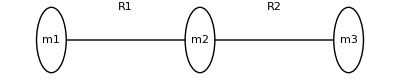

```mathematica
w=.05;
Graphics[{
Text["m1",{0,0}],
Circle[{0,0},w],
Line[{{w,0},{.5-w,0}}],
Text["R1",{.25,w}],
Text["m2",{.5,0}],
Circle[{.5,0},w],
Text["R2",{.75,.05}],
Line[{{.5+w,0},{1-w,0}}],
Text["m3",{1,0}],
Circle[{1,0},w]
}]
```

Kinetic Matrix Function

Classic 2D Colbert and Miller with minor adaptations

LinearThreeMass2DDVRKineticMatrix[grid_, 
	ops:OptionsPattern@{
		"m1"->1,
		"m2"→1,
		"m3"→1,
		"ℏ"->1
		}
	]:=
	Module[
		{
			cartDVR1=
				Cartesian1DDVRKineticMatrix[
					grid[[All, 1, 1]], 
					FilterRules[{
						"M"→1,
						ops
						},
						Options[Cartesian1DDVRKineticMatrix]
						]
					],
			cartDVR2=
				Cartesian1DDVRKineticMatrix[
					grid[[1, All, 2]],
					FilterRules[{
						"M"→1,
						ops
						},
						Options[Cartesian1DDVRKineticMatrix]
						]
					],
			ptsX=Length@grid,
			ptsY=Length@grid[[1]],
			m1=OptionValue["m1"],
			m2=OptionValue["m2"],
			m3=OptionValue["m3"]
			},
		cartDVR1=
			(1/m1)*cartDVR1;
		cartDVR2=
			(1/m3+2/m2)*cartDVR2;
		If[(ptsX*ptsY)>100000,
			ParallelTable,
			Table
			][
			With[
				{
					ix=1+Floor[(i-1)/(ptsY)], jx=1+Floor[(j-1)/(ptsY)],
					iy=Mod[i, ptsY, 1], jy=Mod[j, ptsY, 1]
					},
				If[iy==jy,
						0,
						cartDVR1[[ix, jx]]
						]+
				If[ix==jx,
						0,
						cartDVR2[[iy, jy]]
						]
				],
			{i, ptsX*ptsY},
			{j, ptsX*ptsY}
			]
		]

Potential Matrix Function

This should take the grid generated in grid points function and turn it into the potential energy matrix for the DVR

Options[LinearThreeMass2DDVRPotentialMatrix]={Function->(Norm[(#/2)^2]&)};
LinearThreeMass2DDVRPotentialMatrix[grid_,ops:OptionsPattern[]]:=
	With[{func=OptionValue@Function},
		With[{A=func/@Flatten[grid,1]},
			DiagonalMatrix@A
			]
		]

Plotting Function

Should take the wavefunctions and a scad of options to make a nice plot. Generally reusing some prewritten code works best

Options[LinearThreeMass2DDVRPlotFunction]=
	DeleteDuplicatesBy[First]@
	Flatten@{
		"WavefunctionSelection"→Automatic,
		AxesOrigin->{0,0},
		Scaled→1,
		"ShowEnergy"→True,
		"PotentialStyle"→Automatic,
		"EnergyDigits"->3,
		"ZeroPointEnergy"->0,
		LabelingFunction->Automatic,
		"CutOff"->10^-4,
		Manipulate->True,
		PlotRange->Automatic,
		"SquareWavefunction"->False,
		FilterRules[Options[ListLinePlot],
			Except[AxesOrigin|PlotRange|LabelingFunction]
			]
		};
LinearThreeMass2DDVRPlotFunction[
	solutions_,
	grid2D_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	Module[
		{Λ,X,ψ,
		scale=OptionValue[Scaled],
		num=
			Replace[OptionValue["WavefunctionSelection"],{
				Automatic:>If[TrueQ@OptionValue@Manipulate, All, 1]
				}],
		dataRange,
		potential=
			If[potentialMatrix//MatrixQ,
				Diagonal@potentialMatrix,
				potentialMatrix],
		squared=OptionValue@"SquareWavefunction",
		lf=Replace[OptionValue@LabelingFunction,{
				Automatic->(
					Row@{Subscript["ψ",#1],": E=",
						1.Round[#2, 10^(-OptionValue["EnergyDigits"])]}&),
				None->False}],
		plotWave,
		waveSet,
		Ec=OptionValue["CutOff"],
		wavePlot,potentialPlot,
		λPlot,plotRange,len,
		grid=Flatten[grid2D, 1]
		},
		{Λ,X}=solutions;
		len=Length@X;
		num=
			Replace[num,
				{
					All:>Range[1,len],
					_List:>num,
					_Integer:>Range[1,num],
					_->1
					}];
		ψ=Function[MapThread[Append[#1, If[squared,#2^2,#2]]&,{grid, X[[#]]}]];
		waveSet=ψ/@num;
		dataRange=
			CoordinateBounds@
				Select[Flatten[waveSet,1],Abs[#[[3]]]>=Ec&];
		plotWave[n_]:=
			If[OptionValue["ShowEnergy"]//TrueQ,
				With[{s={1, 1, scale},λ={0,0,Λ[[n]]}},
					λ+s*#&/@ψ[n]
					],
				With[{s={1, 1,scale},λ={0,0,Λ[[n]]}},
					s*#&/@ψ[n]
					]
				];
		waveSet=
			Select[#,
				dataRange[[1,1]]<=#[[1]]≤dataRange[[1,2]]&&
					dataRange[[2,1]]<=#[[2]]≤dataRange[[2,2]]&
				]&/@(plotWave/@num);
		wavePlot[sel_,lFunc_:lf]:=
			ListPlot3D[
				waveSet[[sel]],
				FilterRules[{
					ops,
					PlotRange->
						dataRange,
					PlotLegends->
						If[lFunc===False,
							None,
							(lFunc@@#)&/@
								Thread@{
									num[[ If[IntegerQ@sel,{sel},sel] ]],
									Λ[[ num[[ If[IntegerQ@sel===0,{sel},sel] ]] ]]
									}
							]
					},
					Options@ListLinePlot
					]
				];
		potentialPlot=
			With[{op=OptionValue["PotentialStyle"]},
				If[op===None,
					Nothing,
					ListPlot3D[
						MapThread[Append, {grid,potential}],
						PlotRange->
							dataRange,
						PlotStyle->
							Replace[op,
								Automatic→
									Directive[Opacity[.1], Gray]
								]
						]
					]
				];
		λPlot[sel_]:=
			ListPlot3D[
				MapThread[Append, {grid, ConstantArray[#, Length[grid]]}],
				PlotStyle->Directive[Opacity[.1], Red],
				PlotRange->
					dataRange
				]&/@Λ[[ num[[sel]] ]];
		plotRange=Automatic;
		If[Length@num>1,
			If[OptionValue@Manipulate,
				With[{wp=wavePlot,N=num,
					lF=With[{f=lf[#1,#2]},f&],
					potPlot=potentialPlot,L=Λ,
					λP=λPlot,pR=plotRange},
				Manipulate[
					Show[
						wp[N[[i]],lF],
						{
							potPlot,
							If[OptionValue["ShowEnergy"]//TrueQ,λP[{i}],Sequence@@{}]
							},
						FilterRules[{ops,PlotRange->pR},Options[Plot]]
						],
					{{i,1,""},1,Length@N,1}
					]
				],
				Show[wavePlot[All],
					{potentialPlot,
						If[OptionValue["ShowEnergy"]//TrueQ,
							λPlot[All],
							Sequence@@{}
							]
							},
					FilterRules[{ops,PlotRange->plotRange},
						Options[Plot]
						]
					]
			],
			Show[wavePlot[All],
				{potentialPlot,λPlot[All]},
				FilterRules[{ops,PlotRange->plotRange},
					Options[Plot]
					]
				]
			]
	];

End[];

$LinearThreeMass2DDVR=
	<|
		"Name"→"Linear Three Mass 2D",
		"Dimension"→2,
		"PointLabels"->{"x"|"y"|"z", "x"|"y"|"z"},
		"Range"→{{-10,10}, {-10, 10}},
		"Grid"→Cartesian2DDVRPoints,
		"KineticEnergy"->LinearThreeMass2DDVRKineticMatrix,
		"PotentialEnergy"->Cartesian2DDVRPotentialMatrix,
		"View"->Cartesian2DDVRPlotFunction
		|>

ChemDVREnd[];

$LinearThreeMass2DDVR